```mathematica
Clear["Global`*"];
```

```mathematica
(σ=Import[NotebookDirectory[]<>"CrossSection.xls"][[1,5;;,{12,15,16}]])//TableForm;
σe=Interpolation[σ[[All,{1,2}]],InterpolationOrder->1];
σa=Interpolation[σ[[All,{1,3}]],InterpolationOrder->1];
Show[
ListPlot[{σ[[All,{1,2}]],σ[[All,{1,3}]]},Joined->True,PlotRange->All, ImageSize->Large],Plot[{σe[λ],σa[λ]},{λ, σ[[1,1]], σ[[-1,1]]},PlotRange->All, ImageSize->Large]
];
```

```mathematica
c = 3×10^8; (* m/s *)
τ=1.45×10^-3; (* s *)
NN = 4000; (* ppm *)
NN = 6.62×10^22 NN; (* 1/m^3 *)
h = 6.63×10^-34; (* Постоянная планка *)
Aeff = Pi/4 6^2×10^-12; (* эффективная площадь моды *)
dCore = 6;
dCladding = 125;
Gmm = N[dCore^2/(2 dCladding^2)];
L=1;
λp = 975;
λs = 1100;
Ps = (Aeff h c)/(λs 10^-9);
Pp = (Aeff h c)/(λp 10^-9);
```

```mathematica
{σe[λp],σa[λp],σe[λs],σa[λs]}
```

{1.43×10^-24,1.29×10^-24,1.6×10^-26,4.5×10^-29}

```mathematica
sol=NDSolve[
{0==Gmm×ρp[z](σa[λp] N1[z]-σe[λp] N2[z])-N2[z]/τ,
ρs'[z]==ρs[z](σe[λs] N2[z]-σa[λs] N1[z]),
ρp'[z]==Gmm×ρp[z](σe[λp] N2[z]-σa[λp] N1[z]),
N1[z]+N2[z]==NN, 
Pp ρp[0]==0.6,Ps ρs[0]==1 10^-3},
{ρp,ρs,N1,N2},{z,0,L},AccuracyGoal->Infinity];
```

```mathematica
10Log10[(ρs[L]/.sol)/(ρs[0]/.sol)][[1]]
```

2.50389

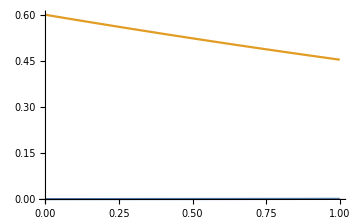
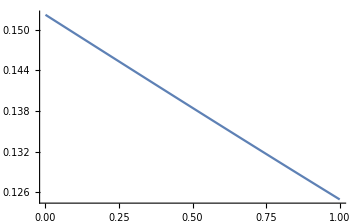

```mathematica
{Plot[Evaluate[{Ps×ρs[z],Pp×ρp[z]}/.sol],{z,0,L},ImageSize->Medium],
Plot[Evaluate[{N2[z]/NN}/.sol],{z,0,L},ImageSize->Medium]}
```